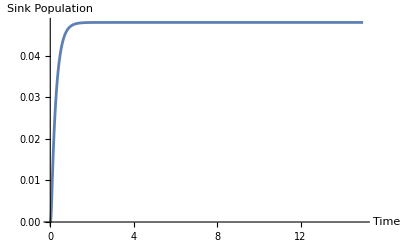

```mathematica
ρvec[t_]={{Λ[t]},{X[t]} ,{Y[t]},{ρNN[t]},{ρ00[t]},{ρsink[t]}};
Γ=2;
γ=3*Pi;
Δ=8; (*ΓN+1*)
No=11; (*Nodes*)
J=3;

s=NDSolve[{(ρvec'[t])[[1]]==-2*(Γ+γ)*(ρvec[t])[[1]]-2*Δ*(ρvec[t])[[2]]+2*γ*(1-(ρvec[t])[[5]]-(ρvec[t])[[6]]),(ρvec'[t])[[2]]==-(2*Γ+2*γ+Δ)*(ρvec[t])[[2]]+(2*γ-Δ)*(ρvec[t])[[4]]-J*No*(ρvec[t])[[3]], (ρvec'[t])[[3]]==-(2*Γ+2*γ+Δ)*(ρvec[t])[[3]]+J*No*(ρvec[t])[[2]]-J*(ρvec[t])[[1]],
(ρvec'[t])[[4]]==-2*(Γ+Δ)*(ρvec[t])[[4]]-2*J*(ρvec[t])[[3]], 
(ρvec'[t])[[5]]==2*Γ*(1-(ρvec[t])[[5]]-(ρvec[t])[[6]]),
(ρvec'[t])[[6]]==2*Δ*(ρvec[t])[[4]],
Λ[0]==1,X[0]==0,Y[0]==0,ρNN[0]==0,ρ00[0]==0,ρsink[0]==0}  ,
{Λ,X,Y,ρNN,ρ00,ρsink},{t,0,20}];
Plot[{Evaluate[ρsink[t]/.s]},{t,0,15},PlotRange->All,AxesLabel->{"Time","Sink Population"}]
```